```mathematica
γ:=0;ε=0.1;tmax=50;
m=1;g=1;l=0.9;ω0=√(g/l);
y[t_]:=ε Sin[2ω0 t+γ]
```

```mathematica
s=First@NDSolve[{θ''[t]==-(g Sin[θ[t]])/(m(l-y[t])),θ[0]==15°,θ'[0]==0},θ,{t,0,tmax}]
```

{θ→InterpolatingFunction[…]}

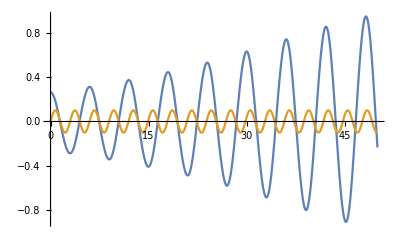

```mathematica
Plot[{θ[t]/.s,y[t]},{t,0,tmax}]
```

```mathematica
Animate[Show[
Graphics[{
GrayLevel[.5],Opacity[.1],Disk[{0,0},0.9,{-30°,-150°}],EdgeForm@Thin,Transparent,Rectangle[{-.8,-1},{.8,0}],
Opacity[1],Line@{{0, 0}, {l*Sin[θ[t]], -l*Cos[θ[t]]}, {(l - y[t])*Sin[θ[t]], -(l - y[t])*Cos[θ[t]]}},
PointSize->Medium,Point[{(l - y[t])*Sin[θ[t]], -(l - y[t])*Cos[θ[t]]}]}]/.s,
ParametricPlot[{(l - y[t1])*Sin[θ[t1]], -(l - y[t1])*Cos[θ[t1]]}/.s,{t1,Max[0,t-30],t},Axes->False]
],{t,0.01,tmax}]
```

```mathematica
plots=Table[Show[
Graphics[{
GrayLevel[.5],Opacity[.1],Disk[{0,0},0.9,{-30°,-150°}],EdgeForm@Thin,Transparent,Rectangle[{-.8,-1},{.8,0}],
Opacity[1],Line@{{0, 0}, {l*Sin[θ[t]], -l*Cos[θ[t]]}, {(l - y[t])*Sin[θ[t]], -(l - y[t])*Cos[θ[t]]}},
PointSize->Medium,Point[{(l - y[t])*Sin[θ[t]], -(l - y[t])*Cos[θ[t]]}]}]/.s,
ParametricPlot[{(l - y[t1])*Sin[θ[t1]], -(l - y[t1])*Cos[θ[t1]]}/.s,{t1,Max[0,t-30],t},Axes->False]
],{t,0.01,tmax,1.25}];
```

```mathematica
Export["C:\\Users\\FangTci\\Desktop\\swing.avi",plots]
```

C:\Users\FangTci\Desktop\swing.avi

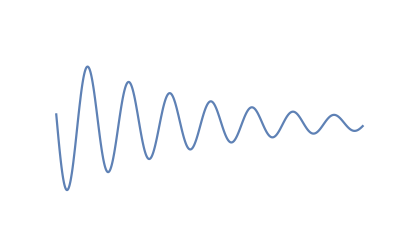

```mathematica
Plot[Sin[x] ⅇ^(-x/20),{x,3,50},PlotRange->{{0,50},{-1.2,1.2}},Axes->False]
```